```mathematica
AsymptoticDSolveValue[{y''[t]+y[t]+ϵ y[t]^3==0,y[0]==1,y'[0]==0},y[t],t,{ϵ,0,1}]
```

Cos[t]+1/32 ϵ (-Cos[t]+Cos[3 t]-12 t Sin[t])

```mathematica
DSolveValue[{y''[t]+ω^2 y[t]==0,y[0]==1,y'[0]==0},y[t],t]
```

Cos[t ω]

```mathematica
y1=DSolveValue[{y''[t]+ω^2 y[t]==-1/4 Cos[3ω t],y[0]==1,y'[0]==0},y[t],t]//TrigReduce
```

(-Cos[t ω]+32 ω^2 Cos[t ω]+Cos[3 t ω])/(32 ω^2)

```mathematica
-3 Cos[ω t]^2 y1+3/4 y1+b Cos[ω t]//TrigReduce//Expand
```

-3/2 Cos[t ω]+b Cos[t ω]+(3 Cos[t ω])/(128 ω^2)-3/4 Cos[3 t ω]-(3 Cos[5 t ω])/(128 ω^2)

```mathematica
SolveValues[-3/2 Cos[t ω]+b Cos[t ω]+(3 Cos[t ω])/(128 ω^2)==0,b][[1]]//Expand
```

3/2-3/(128 ω^2)

```mathematica
DSolveValue[{y''[t]+ω^2 y[t]==-3/4 Cos[3 t ω]-(3 Cos[5 t ω])/(128 ω^2),y[0]==1,y'[0]==0},y[t],t]//FullSimplify
```

(Cos[t ω] (-96 ω^2+512 ω^4+(-1+96 ω^2) Cos[2 t ω]+Cos[4 t ω]))/(512 ω^4)

```mathematica
TrigReduce[Cos[ω t]^3-a Cos[ω t]]
```

1/4 (3 Cos[t ω]-4 a Cos[t ω]+Cos[3 t ω])

```mathematica
Solve[(1+ϵ w1+ϵ^2 w2+O[ϵ]^3)^2-1==3/8 ϵ+(3/2-3/(128 (1+ϵ w1+ϵ^2 w2+O[ϵ]^3)^2)) ϵ^2+O[ϵ]^3,{w1,w2}]
```

{{w1→3/16,w2→369/512}}

```mathematica
(1+ϵ w1+ϵ^2 w2+O[ϵ]^3)^2//Expand
```

1+2 w1 ϵ+(w1^2+2 w2) ϵ^2+O[ϵ]^3

```mathematica
∫_0^T Series[1/(√(1-y^2+1/2 ϵ(1-y^4))),{ϵ,0,1}]ⅆy
```

1/8 T √(1-T^2) ϵ+ArcSin[T]-3/8 ϵ ArcSin[T]

```mathematica
Asymptotic[π/(2AsymptoticIntegrate[1/(√(1+1/2 ϵ(1+Sin[θ]^2))),{θ,0,π/2},{ϵ,0,3}]),{ϵ,0,3}]
```

1+(3 ϵ)/8-(21 ϵ^2)/256+(81 ϵ^3)/2048

```mathematica
Series[1/(√(1+1/2 ϵ(1+Sin[θ]^2))),{ϵ,0,1}]
```

1+1/4 (-1-Sin[θ]^2) ϵ+O[ϵ]^2

```mathematica
4∫_0^(π/2) (1-1/4(1+Sin[θ]^2)ϵ)ⅆθ//Expand
```

2 π-(3 π ϵ)/4

```mathematica
Series[(2π)/(2π-(3π)/4 ϵ),{ϵ,0,2}]
```

1+(3 ϵ)/8+(9 ϵ^2)/64+O[ϵ]^3

```mathematica
AsymptoticDSolveValue[{y''[t]+y[t]-ϵ(1-y[t]^2)y'[t]==0,y[0]==α,y'[0]==β},y[t],t,{ϵ,0,1}]+O[ϵ]//TrigToExp
```

(1/2 (ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)) α+1/2 ⅈ (ⅇ^(-ⅈ t)-ⅇ^(ⅈ t)) β)+O[ϵ]^1

```mathematica
DSolveValue[D[y[t,T], t,t]+y[t,T]==0,y[t,T],{t,T}]
```

Cos[t] C[1][T]+Sin[t] C[2][T]

```mathematica
(ϵ T+t)^2//Expand
```

t^2+2 t T ϵ+T^2 ϵ^2

```mathematica
-ϵ(1-(y0[t,T]+ϵ y1[t,T])^2)(ϵ D[(y0[t,T]+ϵ y1[t,T]), T]+D[(y0[t,T]+ϵ y1[t,T]), t])+O[ϵ]^2//Expand
```

(-1+y0[t,T]^2) y0^(1,0)[t,T] ϵ+O[ϵ]^2

```mathematica
y0=A[T] ⅇ^(ⅈ t)+A[T]*ⅇ^(-ⅈ t);
-2 D[y0, t,T]+(1-y0^2)D[y0, t]//Expand
```

ⅈ ⅇ^(ⅈ t) A[T]-ⅈ ⅇ^(3 ⅈ t) A[T]^3-ⅈ ⅇ^(-ⅈ t) Conjugate[A[T]]-ⅈ ⅇ^(ⅈ t) A[T]^2 Conjugate[A[T]]+ⅈ ⅇ^(-ⅈ t) A[T] Conjugate[A[T]]^2+ⅈ ⅇ^(-3 ⅈ t) Conjugate[A[T]]^3-2 ⅈ ⅇ^(ⅈ t) A'[T]+2 ⅈ ⅇ^(-ⅈ t) A'[T] Conjugate'[A[T]]

```mathematica
-2ⅈ(A'[T] ⅇ^(ⅈ t)-A'[T]*ⅇ^(-ⅈ t))+ⅈ(1-A^2 ⅇ^□)
```

```mathematica
DSolve[A'[T]==1/2 A[T](1-Abs[A[T]]^2),A[T],T]
```

{{A[T]→InverseFunction[1/((-1+Abs[K[1]]) (1+Abs[K[1]]) K[1])K[1]1#1&][-T/2+C[1]]}}

```mathematica
DSolve[{r'[t]==1/2(r[t]-r[t]^3),θ'[t]==0},{r[t],θ[t]},t]
```

{{r[t]→-ⅇ^(t/2)/(√(ⅇ^t+ⅇ^(2 C[1]))),θ[t]→C[2]},{r[t]→ⅇ^(t/2)/(√(ⅇ^t+ⅇ^(2 C[1]))),θ[t]→C[2]}}

```mathematica
y0[t_]=ⅇ^(ⅈ (t+Cθ)) ⅇ^(ϵ/2 t)/(√(ⅇ^(ϵ t)+Cr))+ⅇ^(-ⅈ (t+Cθ))ⅇ^(ϵ/2 t)/(√(ⅇ^(ϵ t)+Cr));
y0[0]//FullSimplify
y0'[0]//FullSimplify
FullSimplify[y0[t]]
```

(2 Cos[Cθ])/(√(1+Cr))

(Cr ϵ Cos[Cθ]-2 (1+Cr) Sin[Cθ])/(1+Cr)^(3/2)

(2 ⅇ^((t ϵ)/2) Cos[Cθ+t])/(√(Cr+ⅇ^(t ϵ)))

```mathematica
AsymptoticDSolveValue[{y''[t]+v1 y[t]+v2 y[t]^2+v3 y[t]^3==0,y[0]==ϵ,y'[0]==0},y[t],t,ϵ->0]
```

$Aborted

```mathematica
Series[V'[y],{y,0,3}]
```

V'[0]+V''[0] y+1/2 V^(3)[0] y^2+1/6 V^(4)[0] y^3+O[y]^4

```mathematica
Solve[JacobiSN[2/π EllipticK[m[0]]θ0,m[0]]==1,θ0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ0→π/2}}

```mathematica
DSolveValue[D[y0[t,T], t,t]+v1 y0[t,T]==0,y0[t,T],{t,T}]
```

Cos[t √v1] C[1][T]+Sin[t √v1] C[2][T]

```mathematica
(t+ϵ T)^2(ϵ y0+ϵ^2 y1+ϵ^3 y2)+v1(ϵ y0+ϵ^2 y1+ϵ^3 y2)+v2(ϵ y0+ϵ^2 y1+ϵ^3 y2)^2+v3(ϵ y0+ϵ^2 y1+ϵ^3 y2)^3+O[ϵ]^4
```

(t^2 y0+v1 y0) ϵ+(2 t T y0+v2 y0^2+t^2 y1+v1 y1) ϵ^2+(T^2 y0+v3 y0^3+2 t T y1+2 v2 y0 y1+t^2 y2+v1 y2) ϵ^3+O[ϵ]^4

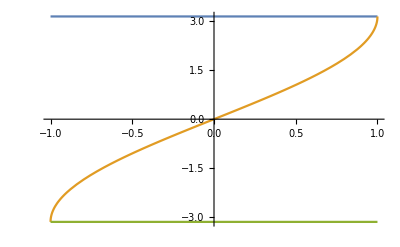

```mathematica
Plot[{π,2ArcSin[x],-π},{x,-1,1}]
```